```mathematica
ClearAll["Global`*"]
```

```mathematica
table1p5nF = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\C1,5nF_2019_09_02_16_31_52.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable=Delete[table1p5nF, 1];
```

```mathematica
table150pF = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\C150pF_2019_09_02_16_40_03.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable1=Delete[table150pF, 1];
```

```mathematica
table2p2mkF = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\C2,2mkF_2019_09_02_16_47_31.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable2=Delete[table2p2mkF, 1];
```

```mathematica
newtable3 = Delete[table150plus, 1];
```

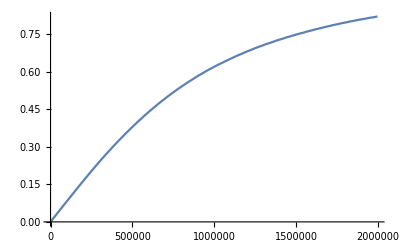

```mathematica
ListLinePlot[table1p5nF]
```

```mathematica
ZparallelRC[R_, C_, ω_] := (R×1/(ⅈ×ω×C))/(R+1/(ⅈ×ω×C))
```

```mathematica
N[ZparallelRC[46.5, 25*10^-12, ω]]
```

-(0.+1.86×10^12 ⅈ)/((46.5-(0.+4.×10^10 ⅈ)/ω) ω)

```mathematica
ZC[ω_, Rp_, C0_, Rs_, Ls_]:=50+ⅈ×ω×Ls+ZparallelRC[Rp, C0, ω]+Rs+ZparallelRC[46.5, 25×10^-12, ω]
```

```mathematica
(*Zreal[ω_,  Rp_, C0_, Rs_] := 50 + Rp/(1+Rp^2*ω^2*C0^2)+  Rs + 46.5/(1+46.5^2*ω^2*(25*10^-12)^2)*)
```

```mathematica
(*Zim[ω_, Ls_, Rp_, C0_]:=ω*Ls-(ω*Rp^2*C0)/(1+Rp^2*ω*C0^2)-(ω*46.5^2*(25*10^-12))/(1+46.5^2*ω*(25*10^-12)^2)*)а
```

а

```mathematica
AbsZ[ω_, Rp_, C0_, Rs_, Ls_]:=√(Zim[2π×ω, Ls, Rp, C0]^2+Zreal[2π×ω,  Rp, C0, Rs]^2)
```

```mathematica
Uin[ω_, Ls_, Rp_, C0_, Rs_]:=2*Re[Abs[ZparallelRC[46.5, 25*10^-12, 2π×ω]]/Abs[ZC[2π×ω, Rp, C0, Rs, Ls]]]
```

```mathematica
(*Manipulate[Show[Plot[Uin[ω, Ls, Rp, 1.5*10^-9, Rs],{ω,Min[newtable[[All,1]]],Max[newtable[[All,1]]]}],ListLinePlot[newtable, PlotStyle->Green]], {Ls, 10^-12, 10^-5}, {Rp, 10^5, 10^12}, {Rs, 10^-12, 10^-5}]*)
```

```mathematica
(*Manipulate[Show[Plot[Uin[ω, Ls, Rp, 150*10^-12, Rs],{ω,Min[newtable[[All,1]]],Max[newtable[[All,1]]]}],ListLinePlot[newtable1, PlotStyle->Green]], {Ls, 10^-12, 10^-5}, {Rp, 10^5, 10^12}, {Rs, 10^-12, 10^-5}]*)
```

```mathematica
(*Manipulate[Show[Plot[Uin[ω, Ls, Rp, 2.2*10^-6, Rs],{ω,Min[newtable2[[All,1]]],Max[newtable2[[All,1]]]}],ListLinePlot[newtable2, PlotStyle->Green]], {Ls, 10^-12, 10^-5}, {Rp, 10^4, 10^12}, {Rs, 10^-12, 10^-5}]*)
```

```mathematica
fit1p5= FindFit[newtable, Uin[ω, Ls, Rp, C0, Rs], {{Ls,10^-6}, {Rp,10^5}, {C0,1.5*10^-9}, {Rs, 10^-6}}, ω,MaxIterations->10000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Ls→5.38582×10^-7,Rp→3.27504×10^7,C0→1.41717×10^-9,Rs→5.77458}

```mathematica
fit150= FindFit[newtable1, Uin[ω, Ls, Rp, C0, Rs], {{Ls, 10^-6}, {Rp, 10^5}, {C0,150*10^-12}, {Rs, 10^-5}}, ω,MaxIterations->1000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Ls→9.82663×10^-7,Rp→463089.,C0→1.51697×10^-10,Rs→43.1451}

```mathematica
fit2p2= FindFit[newtable2, Uin[ω, Ls, Rp, C0, Rs], {{Ls, 10^-6}, {Rp, 10^7}, {C0,2.2*10^-6}, {Rs, 10^-5}}, ω,MaxIterations->10000]
```

{Ls→0.0000859548,Rp→6.82686×10^10,C0→2.12857×10^-6,Rs→2.468}

```mathematica
fit150plus = FindFit[newtable3, Uin[ω, Ls, Rp, C0, Rs], {{Ls, 10^-6}, {Rp, 10^5}, {C0,150*10^-12}, {Rs, 10^-5}}, ω,MaxIterations->1000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Ls→9.55773×10^-7,Rp→-84440.2,C0→1.47246×10^-10,Rs→2.83147}

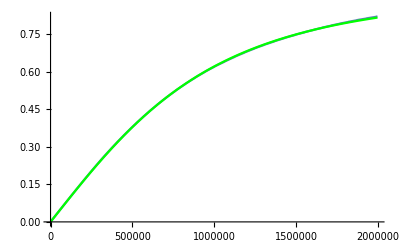

```mathematica
Show[ListLinePlot[newtable],
Plot[Uin[ω,Ls,Rp,C0,Rs]/.fit1p5,{ω,Min[newtable[[All,1]]],Max[newtable[[All,1]]]},PlotStyle->Green]]
```

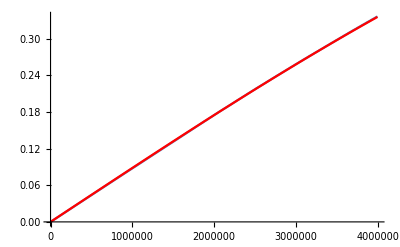

```mathematica
Show[ListLinePlot[newtable1],Plot[Uin[ω,Ls,Rp,C0,Rs]/.fit150,{ω,Min[newtable1[[All,1]]],Max[newtable1[[All,1]]]},PlotStyle->Red]]
```

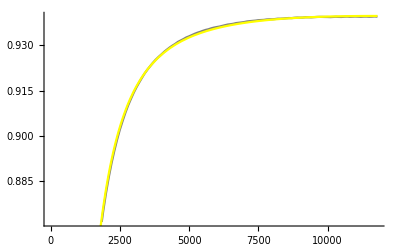

```mathematica
Show[ListLinePlot[newtable2, PlotStyle->Gray],Plot[Uin[ω,Ls,Rp,C0,Rs]/.fit2p2,{ω,Min[newtable2[[All,1]]],Max[newtable2[[All,1]]]},PlotStyle->Yellow]]
```

```mathematica
(*nlm=NonlinearModelFit[newtable, Uin[ω, Ls, Rp, C0, Rs], {Ls, Rp, {C0,1.5*10^-9}, Rs}, ω,MaxIterations->10000]*)
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[5.92056×10^11 Re[Abs[1/((46.5-(20000000000 ⅈ)/(π ω)) ω)]/Abs[123.819-(0.+«19» ⅈ)/((«18»-(«1»)/ω) ω)-(0.+«1»)/((«1») ω)+(0.+3.18805×10^-7 ⅈ) ω]]]

```mathematica
(*nlm["ParameterTable"]*)
```

| Estimate | Standard Error | t-Statistic | P-Value
Ls | 5.07394×10^-8 | 0.00322026 | 0.0000157563 | 0.999987
Rp | 196144. | 0. | ∞ | 0.
C0 | 1.738 | 0. | ∞ | 0.
Rs | 73.8187 | 5.52047 | 13.3718 | 6.49424×10^-34